```mathematica
(*Test func*)
(*side_: Triangle side length *)
(*trans_: 2D vector *)
(*rot_: Angle *)
createMeasurementPoints[side_, trans_, rot_] :=Module[{localPoints, transform, measure, sides, transformedPoints},
localPoints = Array[RotationTransform[# * 120°][{0, side/√3}] &, 3];
transform =TranslationTransform[trans].RotationTransform[rot ]; 
transformedPoints = transform[localPoints];
measure = Interpolation[Array[{#-1, transformedPoints[[Mod[# , 3]+1 ]]}&, 4], InterpolationOrder ->1];
sides = Array[measure@RandomReal[{#-1, #}, 2]&,3];
Return[sides];
];
```

```mathematica
(*Compute hole coordinates from 6 measurement points, 2 for each side*)
(*dist_: Hole distance *)
(*points_: 3 x 2 array of 2D points *)
getHoles[dist_, points_] := Module[{eqs, sol, vertices, origin, yAxis, xAxis, holes},
eqs = Map[RotationTransform[90°][#[[1]]-#[[2]]].({x, y}-#[[2]]) == 0 &, points];
sol =Solve[#, {x, y}]&/@Partition[eqs, 2, 1, 1];
vertices = ({x,y} /.#) &/@ Flatten[sol, 1];
origin = Plus @@vertices / 3;
yAxis = vertices[[1]] - origin;
xAxis = RotationTransform[-90°][yAxis];
holes  = Array[RotationTransform[#*120°][dist/√3*Normalize[yAxis]]+origin &, 3];
Return[{origin, vertices,holes}];
];
```

{{{12.76,-34.81},{65.13,-138.175}},{{153.18,-138.175},{232.555,-16.58}},{{275.59,124.315},{222.64,126.82}}}

{{116.791,16.3047},{{103.606,-214.117},{323.063,122.069},{-76.2952,140.962}},{{245.71,81.2147},{-3.88182,95.4966},{108.546,-127.797}}}

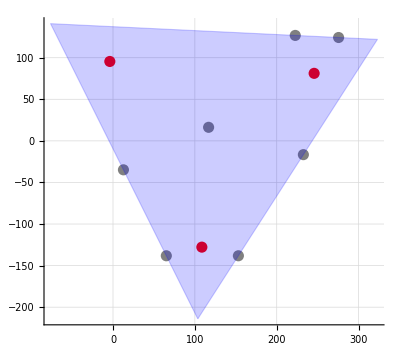

```mathematica
(*translation = {RandomReal[{-100, 100}], RandomReal[{-100, 100}]};
rotation = RandomReal[{0, 360}];
points = createMeasurementPoints[380, translation, rotation]*)
points={
{{12.76,-34.81},{65.13,-138.175}},
{{153.18,-138.175},{232.555,-16.58}},
{{275.59,124.315},{222.64,126.82}}
}

{center, vertices, holes} = getHoles[250, points]

Graphics[{PointSize[0.02], Gray,Point[Flatten[points, 1]], Point[center],Red, Point[holes], Opacity[0.2], Blue, EdgeForm[Thick] ,Triangle[vertices]}, Axes->True, GridLines->Automatic]
```